```mathematica
CheckSuffMProperty[A0_]:=Module[{A=A0,B=A0-DiagonalMatrix[Diagonal[A0]],M=1},
If[Total[UnitStep[-Diagonal[A]]]>0,M=0;Print["Diagonal <= 0"]];
If[Total[1-UnitStep[-Flatten[B]]]>0,M=0;Print["Off-Diagonal > 0"]];
If[Total[Tally[Sign[Total[Transpose[A]]]]][[1]]≠1&&Total[Tally[Sign[Total[A]]]][[1]],M=0;Print["Not Diagonally Dominant"]];
M
]
```

```mathematica
LCPiterate[M0_,q0_,x0_,t0_,norm0_,LCPsolver_]:=(*Iterative LCP Solver*)
Module[{M=M0,q=q0,n=Length[x0],norm=norm0,x=x0,tol=t0,notDone=True,d=M0.x0-q0,LCP=LCPsolver,i,xm=0},

While[notDone||Min[d]<-tol xm||Min[x]<-tol xm,
Print["LCP iteration"];
Print[Timing[x=LCPsolver[M,q,d,x];][[1]]];

(*Check for termination*)
d=M.x-q;
xm=Norm[x,norm];
i=1;notDone=False;
While[!notDone &&i≤n,
notDone=Abs[d[[i]]]>tol xm && Abs[x[[i]]]>tol xm ;
(*If[notDone,Print[Min[Abs[d[[i]]]/bm,Abs[x[[i]]-c[[i]]]/ cm]]];*)
i++
]

(*Print[{Min[d]/bm,Min[x-c]/cm}];*)

];
x
(*ListLinePlot[{M.x-q,x}]*)
];
```

```mathematica
PIM[M0_,q0_,d0_,x0_]:=(*Policy Iteration Method*)Module[{M=M0,q=q0,d=d0,x=x0,n=Length[x0],i,k},

d-=x;

Print[Timing[
(*Construct the Matrix for the current iteration*)
For[i=1,i≤n,i++,
If[d[[i]]≥0,
For[k=1, k≤n,k++,
M[[i,k]]=KroneckerDelta[i,k];
];
q[[i]]=0
];
];][[1]]];
Print[Timing[x=LinearSolve[M,q];][[1]]];
x
];
```

```mathematica
(*Generation of a some random M-Matrix*)
n=10;
b=Join[{0},-RandomReal[10,n-1]];
c=Join[-RandomReal[10,n-1],{0}];
a=-b-c+(Max[0,#]&/@(5*(RandomReal[1,n]-0.6))^2);
```

1

1

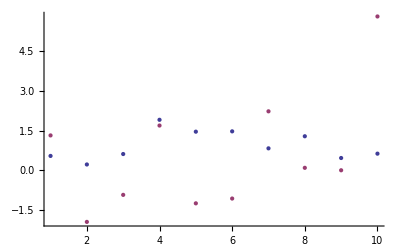

```mathematica
M1=SparseArray[{{i_,i_}:>a[[i]],{i_,j_}/;i-j==1:>b[[i]],{i_,j_}/;j-i==1:>c[[i]]},{n,n}];
M2=SparseArray[{{i_,i_}->2.1,{i_,j_}/;i-j==-1->-1.0,{i_,j_}/;i-j==-1->-1.01},{n,n}];
CheckSuffMProperty[M1]
CheckSuffMProperty[M2]
x=RandomReal[2,n];q=Table[N[2Sin[20 i/n]+PolyLog[0,2(i-1)/n-1]],{i,n}];
ListPlot[{x,q}]
```

```mathematica
n=100;q=Table[Sin[0.1i],{i,n}];z=Table[0.005 i,{i,n}];M2=SparseArray[{{i_,i_}->i^0.3*2.0,{i_,j_}/;i-j==-1->-0.5j^0.3,{i_,j_}/;i-j==1->-0.5+0.9Sin[i]},{n,n}];
```

$Aborted

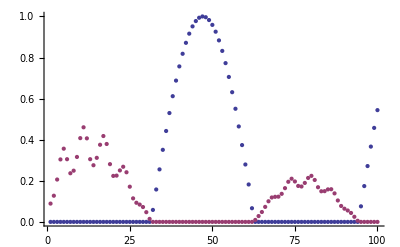

```mathematica
ListPlot[{M2.a2-q,a2},PlotRange->All]
```

```mathematica
a2=LCPiterate[M2,q,z,10^-15,Infinity,PIM];a2[[1;;Min[n,100]]]
```

LCP iteration

0.047

0.

0.047

LCP iteration

0.031

0.

0.031

{0.0891247,0.127387,0.206228,0.304068,0.356352,0.305145,0.236776,0.249314,0.316122,0.407697,0.460383,0.406635,0.305151,0.275756,0.311821,0.375463,0.417935,0.379243,0.281051,0.223842,0.225313,0.250573,0.268422,0.241562,0.171369,0.114525,0.0931236,0.0843046,0.0723399,0.0472598,0.0147051,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00955177,0.0283699,0.048115,0.0731036,0.100327,0.118832,0.122094,0.122773,0.136593,0.164166,0.195272,0.210159,0.196779,0.174995,0.172334,0.189669,0.213902,0.224131,0.204092,0.168727,0.149038,0.149628,0.158176,0.15899,0.138785,0.104272,0.0775718,0.0642821,0.0555079,0.043539,0.0249099,0.00546702,0.,0.,0.,0.,0.,0.}

```mathematica
LCPiterate[M0_,a0_,b0_,c0_,q0_,x0_,t0_,norm0_,LCPsolver_]:=(*Iterative MTA Solver*)
Module[{M=M0,a=a0,b=b0,c=c0,q=q0,n=Length[x0],norm=norm0,x=x0,tol=t0,notDone=True,d=M0.x0-q0,LCP=LCPsolver,i,xm=0},

While[notDone||Min[d]<-tol xm||Min[x]<-tol xm,
Print["LCP iteration"];
Print[Timing[x=LCPsolver[a,b,c,q,x];][[1]]];

(*Check for termination*)
d=M.x-q;
xm=Norm[x,norm];
i=1;notDone=False;
While[!notDone &&i≤n,
notDone=Abs[d[[i]]]>tol xm && Abs[x[[i]]]>tol xm ;
(*If[notDone,Print[Min[Abs[d[[i]]]/bm,Abs[x[[i]]-c[[i]]]/ cm]]];*)
i++
]

(*Print[{Min[d]/bm,Min[x-c]/cm}];*)

];
ListLinePlot[{M.x-q,x}]
];
```

```mathematica
MTA[a0_,b0_,c0_,q0_,x0_]:=(*MODIFIED_THOMAS_ALGORITHM*)
Module[{β=a0,α=b0,γ=c0,b=q0,x=x0,n=Length[x0],i,k,λ},

If[x[[1]](β[[1]]-1)+x[[2]]γ[[1]]≥ 0,β[[i]]=1;γ[[i]]=0;b[[i]]=0];

For[i=2,i≤n,i++,
If[x[[i-1]]α[[i]]+x[[i]](β[[i]]-1)+x[[i+1]]γ[[i]]<0,
λ=α[[i]]/β[[i-1]];
β[[i]]-=λ γ[[i-1]];
b[[i]]-=λ b[[i-1]],
β[[i]]=1;γ[[i]]=0;b[[i]]=0
]];
x[[n]]=q[[n]]/a[[n]];
For[i=1,i<n,i++,x[[i]]=(q[[i]]-c[[i]]x[[i+1]])/a[[i]]];
]
```